```mathematica
ket0={{1},{0}};
ket1={{0},{1}};
Id=IdentityMatrix[2];
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];
H=HadamardMatrix[2];
Ry[θ_]:=MatrixExp[-ⅈ θ Y/2];
Rx[θ_]:=MatrixExp[-ⅈ θ X/2];
Rz[θ_]:=MatrixExp[-ⅈ θ Z/2];
CNOT[c_,t_,n_]:=KroneckerProduct[IdentityMatrix[2^c],ket0.ket0†,IdentityMatrix[2^(n-1-c)]]+KroneckerProduct[IdentityMatrix[2^c],ket1.ket1†,IdentityMatrix[2^(n-1-c)]].KroneckerProduct[IdentityMatrix[2^t],X,IdentityMatrix[2^(n-1-t)]];
CU[c_,t_,n_,U_]:=KroneckerProduct[IdentityMatrix[2^c],ket0.ket0†,IdentityMatrix[2^(n-1-c)]]+KroneckerProduct[IdentityMatrix[2^c],ket1.ket1†,IdentityMatrix[2^(n-1-c)]].KroneckerProduct[IdentityMatrix[2^t],U,IdentityMatrix[2^(n-Log2[Dimensions[U][[1]]]-t)]];
P0=ket0.ket0†;
P1=ket1.ket1†;
```

```mathematica
MatrixExp[-ⅈ θ Z/2]//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

```mathematica
R=KroneckerProduct[Id,Id,X].CNOT[2,1,3].CU[2,0,3,CNOT[1,0,3]];
R.KroneckerProduct[ket1,ket1,ket1]
```

{{1},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
R2=KroneckerProduct[Id,X].CNOT[1,0,2];
Zp=X.PauliMatrix[3].X;
α=0.85;
n=4;
β=(1-α)/n;
γ=α/3+β;

θ0=ArcCos[√(1-γ)];
θ1=ArcCos[1/2];

T1=(KroneckerProduct[P0,P1,R2†-KroneckerProduct[Id,Id]]+KroneckerProduct[Id,Id,Id,Id]);
T1=(KroneckerProduct[P1,P0,R2†.R2†-KroneckerProduct[Id,Id]]+KroneckerProduct[Id,Id,Id,Id]).T1;

Kb2=(KroneckerProduct[P1,P1,KroneckerProduct[H,H]-KroneckerProduct[Id,Id]]+KroneckerProduct[Id,Id,Id,Id]);

Kb1=(KroneckerProduct[Id,Id]+KroneckerProduct[P1,-Id+Ry[θy10]]).(KroneckerProduct[Id,Id]+KroneckerProduct[P0,-Id+Ry[θy00]]).(KroneckerProduct[Id,Id]+KroneckerProduct[-Id+Ry[θy01],P0])/.{θy00->-1.900220607202805 2,θy01->-2.212560440981948 2,θy10->-0.75 π 2};
Kb1=(KroneckerProduct[P1,P1,Kb1†-KroneckerProduct[Id,Id]]+KroneckerProduct[Id,Id,Id,Id]).KroneckerProduct[Id,Id,Kb1];

Dd=(KroneckerProduct[Id,Id,P0,Zp-Id]+KroneckerProduct[Id,Id,Id,Id]);

SWAP=(KroneckerProduct[Id,ket0,Id,ket1].KroneckerProduct[Id,ket1,Id,ket0]†+KroneckerProduct[Id,ket1,Id,ket0].KroneckerProduct[Id,ket0,Id,ket1]†+KroneckerProduct[Id,P0,Id,P0]+KroneckerProduct[Id,P1,Id,P1]);
SWAP=(KroneckerProduct[ket0,Id,ket1,Id].KroneckerProduct[ket1,Id,ket0,Id]†+KroneckerProduct[ket1,Id,ket0,Id].KroneckerProduct[ket0,Id,ket1,Id]†+KroneckerProduct[P0,Id,P0,Id]+KroneckerProduct[P1,Id,P1,Id]).SWAP;

Uwalk=SWAP.T1†.Kb2.Kb1.Dd.Kb1†.Kb2†.T1;
```

```mathematica
W={{0.8556250000000001,-0.2029210514584428,-0.2029210514584428,-0.2029210514584428,-0.0786090559703878,0.048124999999999994,0.14076505371441525,0.14076505371441525,-0.0786090559703878,0.14076505371441525,0.048124999999999994,0.14076505371441525,-0.10968705484240152,0.10968705484240152,0.10968705484240152,0.10968705484240152},{-0.0786090559703878,0.1284027777777779,-0.2299305555555556,-0.2299305555555556,0.048124999999999994,-0.2029210514584428,0.048124999999999994,0.048124999999999994,0.4117361111111109,-0.2299305555555556,0.14076505371441525,0.4117361111111109,0.32083333333333325,-0.32083333333333325,0.32083333333333325,0.32083333333333325},{-0.0786090559703878,-0.2299305555555556,0.1284027777777779,-0.2299305555555556,0.4117361111111109,0.14076505371441525,-0.2299305555555556,0.4117361111111109,0.048124999999999994,0.048124999999999994,-0.2029210514584428,0.048124999999999994,0.32083333333333325,0.32083333333333325,-0.32083333333333325,0.32083333333333325},{-0.10968705484240152,-0.32083333333333325,-0.32083333333333325,0.17916666666666675,0.32083333333333325,0.10968705484240152,0.32083333333333325,-0.17916666666666675,0.32083333333333325,0.32083333333333325,0.10968705484240152,-0.17916666666666675,0.25,0.25,0.25,-0.25},{-0.2029210514584428,0.048124999999999994,0.048124999999999994,0.048124999999999994,0.1284027777777779,-0.0786090559703878,-0.2299305555555556,-0.2299305555555556,-0.2299305555555556,0.4117361111111109,0.14076505371441525,0.4117361111111109,-0.32083333333333325,0.32083333333333325,0.32083333333333325,0.32083333333333325},{0.048124999999999994,-0.0786090559703878,0.14076505371441525,0.14076505371441525,-0.2029210514584428,0.8556250000000001,-0.2029210514584428,-0.2029210514584428,0.14076505371441525,-0.0786090559703878,0.048124999999999994,0.14076505371441525,0.10968705484240152,-0.10968705484240152,0.10968705484240152,0.10968705484240152},{0.14076505371441525,0.4117361111111109,-0.2299305555555556,0.4117361111111109,-0.2299305555555556,-0.0786090559703878,0.1284027777777779,-0.2299305555555556,0.048124999999999994,0.048124999999999994,-0.2029210514584428,0.048124999999999994,0.32083333333333325,0.32083333333333325,-0.32083333333333325,0.32083333333333325},{0.10968705484240152,0.32083333333333325,0.32083333333333325,-0.17916666666666675,-0.32083333333333325,-0.10968705484240152,-0.32083333333333325,0.17916666666666675,0.32083333333333325,0.32083333333333325,0.10968705484240152,-0.17916666666666675,0.25,0.25,0.25,-0.25},{-0.2029210514584428,0.048124999999999994,0.048124999999999994,0.048124999999999994,-0.2299305555555556,0.14076505371441525,0.4117361111111109,0.4117361111111109,0.1284027777777779,-0.2299305555555556,-0.0786090559703878,-0.2299305555555556,-0.32083333333333325,0.32083333333333325,0.32083333333333325,0.32083333333333325},{0.14076505371441525,-0.2299305555555556,0.4117361111111109,0.4117361111111109,0.048124999999999994,-0.2029210514584428,0.048124999999999994,0.048124999999999994,-0.2299305555555556,0.1284027777777779,-0.0786090559703878,-0.2299305555555556,0.32083333333333325,-0.32083333333333325,0.32083333333333325,0.32083333333333325},{0.048124999999999994,0.14076505371441525,-0.0786090559703878,0.14076505371441525,0.14076505371441525,0.048124999999999994,-0.0786090559703878,0.14076505371441525,-0.2029210514584428,-0.2029210514584428,0.8556250000000001,-0.2029210514584428,0.10968705484240152,0.10968705484240152,-0.10968705484240152,0.10968705484240152},{0.10968705484240152,0.32083333333333325,0.32083333333333325,-0.17916666666666675,0.32083333333333325,0.10968705484240152,0.32083333333333325,-0.17916666666666675,-0.32083333333333325,-0.32083333333333325,-0.10968705484240152,0.17916666666666675,0.25,0.25,0.25,-0.25},{-0.2029210514584428,0.048124999999999994,0.048124999999999994,0.048124999999999994,-0.2299305555555556,0.14076505371441525,0.4117361111111109,0.4117361111111109,-0.2299305555555556,0.4117361111111109,0.14076505371441525,0.4117361111111109,0.17916666666666675,-0.17916666666666675,-0.17916666666666675,-0.17916666666666675},{0.14076505371441525,-0.2299305555555556,0.4117361111111109,0.4117361111111109,0.048124999999999994,-0.2029210514584428,0.048124999999999994,0.048124999999999994,0.4117361111111109,-0.2299305555555556,0.14076505371441525,0.4117361111111109,-0.17916666666666675,0.17916666666666675,-0.17916666666666675,-0.17916666666666675},{0.14076505371441525,0.4117361111111109,-0.2299305555555556,0.4117361111111109,0.4117361111111109,0.14076505371441525,-0.2299305555555556,0.4117361111111109,0.048124999999999994,0.048124999999999994,-0.2029210514584428,0.048124999999999994,-0.17916666666666675,-0.17916666666666675,0.17916666666666675,-0.17916666666666675},{0.10968705484240152,0.32083333333333325,0.32083333333333325,-0.17916666666666675,0.32083333333333325,0.10968705484240152,0.32083333333333325,-0.17916666666666675,0.32083333333333325,0.32083333333333325,0.10968705484240152,-0.17916666666666675,-0.25,-0.25,-0.25,0.25}};
Uwalk.Uwalk//MatrixForm
W//MatrixForm
Norm[Uwalk.Uwalk-W]
```

(0.855625 | -0.202921 | -0.202921 | -0.202921 | -0.0786091 | 0.048125 | 0.140765 | 0.140765 | -0.0786091 | 0.140765 | 0.048125 | 0.140765 | -0.109687 | 0.109687 | 0.109687 | 0.109687
-0.0786091 | 0.128403 | -0.229931 | -0.229931 | 0.048125 | -0.202921 | 0.048125 | 0.048125 | 0.411736 | -0.229931 | 0.140765 | 0.411736 | 0.320833 | -0.320833 | 0.320833 | 0.320833
-0.0786091 | -0.229931 | 0.128403 | -0.229931 | 0.411736 | 0.140765 | -0.229931 | 0.411736 | 0.048125 | 0.048125 | -0.202921 | 0.048125 | 0.320833 | 0.320833 | -0.320833 | 0.320833
-0.109687 | -0.320833 | -0.320833 | 0.179167 | 0.320833 | 0.109687 | 0.320833 | -0.179167 | 0.320833 | 0.320833 | 0.109687 | -0.179167 | 0.25 | 0.25 | 0.25 | -0.25
-0.202921 | 0.048125 | 0.048125 | 0.048125 | 0.128403 | -0.0786091 | -0.229931 | -0.229931 | -0.229931 | 0.411736 | 0.140765 | 0.411736 | -0.320833 | 0.320833 | 0.320833 | 0.320833
0.048125 | -0.0786091 | 0.140765 | 0.140765 | -0.202921 | 0.855625 | -0.202921 | -0.202921 | 0.140765 | -0.0786091 | 0.048125 | 0.140765 | 0.109687 | -0.109687 | 0.109687 | 0.109687
0.140765 | 0.411736 | -0.229931 | 0.411736 | -0.229931 | -0.0786091 | 0.128403 | -0.229931 | 0.048125 | 0.048125 | -0.202921 | 0.048125 | 0.320833 | 0.320833 | -0.320833 | 0.320833
0.109687 | 0.320833 | 0.320833 | -0.179167 | -0.320833 | -0.109687 | -0.320833 | 0.179167 | 0.320833 | 0.320833 | 0.109687 | -0.179167 | 0.25 | 0.25 | 0.25 | -0.25
-0.202921 | 0.048125 | 0.048125 | 0.048125 | -0.229931 | 0.140765 | 0.411736 | 0.411736 | 0.128403 | -0.229931 | -0.0786091 | -0.229931 | -0.320833 | 0.320833 | 0.320833 | 0.320833
0.140765 | -0.229931 | 0.411736 | 0.411736 | 0.048125 | -0.202921 | 0.048125 | 0.048125 | -0.229931 | 0.128403 | -0.0786091 | -0.229931 | 0.320833 | -0.320833 | 0.320833 | 0.320833
0.048125 | 0.140765 | -0.0786091 | 0.140765 | 0.140765 | 0.048125 | -0.0786091 | 0.140765 | -0.202921 | -0.202921 | 0.855625 | -0.202921 | 0.109687 | 0.109687 | -0.109687 | 0.109687
0.109687 | 0.320833 | 0.320833 | -0.179167 | 0.320833 | 0.109687 | 0.320833 | -0.179167 | -0.320833 | -0.320833 | -0.109687 | 0.179167 | 0.25 | 0.25 | 0.25 | -0.25
-0.202921 | 0.048125 | 0.048125 | 0.048125 | -0.229931 | 0.140765 | 0.411736 | 0.411736 | -0.229931 | 0.411736 | 0.140765 | 0.411736 | 0.179167 | -0.179167 | -0.179167 | -0.179167
0.140765 | -0.229931 | 0.411736 | 0.411736 | 0.048125 | -0.202921 | 0.048125 | 0.048125 | 0.411736 | -0.229931 | 0.140765 | 0.411736 | -0.179167 | 0.179167 | -0.179167 | -0.179167
0.140765 | 0.411736 | -0.229931 | 0.411736 | 0.411736 | 0.140765 | -0.229931 | 0.411736 | 0.048125 | 0.048125 | -0.202921 | 0.048125 | -0.179167 | -0.179167 | 0.179167 | -0.179167
0.109687 | 0.320833 | 0.320833 | -0.179167 | 0.320833 | 0.109687 | 0.320833 | -0.179167 | 0.320833 | 0.320833 | 0.109687 | -0.179167 | -0.25 | -0.25 | -0.25 | 0.25)

(0.855625 | -0.202921 | -0.202921 | -0.202921 | -0.0786091 | 0.048125 | 0.140765 | 0.140765 | -0.0786091 | 0.140765 | 0.048125 | 0.140765 | -0.109687 | 0.109687 | 0.109687 | 0.109687
-0.0786091 | 0.128403 | -0.229931 | -0.229931 | 0.048125 | -0.202921 | 0.048125 | 0.048125 | 0.411736 | -0.229931 | 0.140765 | 0.411736 | 0.320833 | -0.320833 | 0.320833 | 0.320833
-0.0786091 | -0.229931 | 0.128403 | -0.229931 | 0.411736 | 0.140765 | -0.229931 | 0.411736 | 0.048125 | 0.048125 | -0.202921 | 0.048125 | 0.320833 | 0.320833 | -0.320833 | 0.320833
-0.109687 | -0.320833 | -0.320833 | 0.179167 | 0.320833 | 0.109687 | 0.320833 | -0.179167 | 0.320833 | 0.320833 | 0.109687 | -0.179167 | 0.25 | 0.25 | 0.25 | -0.25
-0.202921 | 0.048125 | 0.048125 | 0.048125 | 0.128403 | -0.0786091 | -0.229931 | -0.229931 | -0.229931 | 0.411736 | 0.140765 | 0.411736 | -0.320833 | 0.320833 | 0.320833 | 0.320833
0.048125 | -0.0786091 | 0.140765 | 0.140765 | -0.202921 | 0.855625 | -0.202921 | -0.202921 | 0.140765 | -0.0786091 | 0.048125 | 0.140765 | 0.109687 | -0.109687 | 0.109687 | 0.109687
0.140765 | 0.411736 | -0.229931 | 0.411736 | -0.229931 | -0.0786091 | 0.128403 | -0.229931 | 0.048125 | 0.048125 | -0.202921 | 0.048125 | 0.320833 | 0.320833 | -0.320833 | 0.320833
0.109687 | 0.320833 | 0.320833 | -0.179167 | -0.320833 | -0.109687 | -0.320833 | 0.179167 | 0.320833 | 0.320833 | 0.109687 | -0.179167 | 0.25 | 0.25 | 0.25 | -0.25
-0.202921 | 0.048125 | 0.048125 | 0.048125 | -0.229931 | 0.140765 | 0.411736 | 0.411736 | 0.128403 | -0.229931 | -0.0786091 | -0.229931 | -0.320833 | 0.320833 | 0.320833 | 0.320833
0.140765 | -0.229931 | 0.411736 | 0.411736 | 0.048125 | -0.202921 | 0.048125 | 0.048125 | -0.229931 | 0.128403 | -0.0786091 | -0.229931 | 0.320833 | -0.320833 | 0.320833 | 0.320833
0.048125 | 0.140765 | -0.0786091 | 0.140765 | 0.140765 | 0.048125 | -0.0786091 | 0.140765 | -0.202921 | -0.202921 | 0.855625 | -0.202921 | 0.109687 | 0.109687 | -0.109687 | 0.109687
0.109687 | 0.320833 | 0.320833 | -0.179167 | 0.320833 | 0.109687 | 0.320833 | -0.179167 | -0.320833 | -0.320833 | -0.109687 | 0.179167 | 0.25 | 0.25 | 0.25 | -0.25
-0.202921 | 0.048125 | 0.048125 | 0.048125 | -0.229931 | 0.140765 | 0.411736 | 0.411736 | -0.229931 | 0.411736 | 0.140765 | 0.411736 | 0.179167 | -0.179167 | -0.179167 | -0.179167
0.140765 | -0.229931 | 0.411736 | 0.411736 | 0.048125 | -0.202921 | 0.048125 | 0.048125 | 0.411736 | -0.229931 | 0.140765 | 0.411736 | -0.179167 | 0.179167 | -0.179167 | -0.179167
0.140765 | 0.411736 | -0.229931 | 0.411736 | 0.411736 | 0.140765 | -0.229931 | 0.411736 | 0.048125 | 0.048125 | -0.202921 | 0.048125 | -0.179167 | -0.179167 | 0.179167 | -0.179167
0.109687 | 0.320833 | 0.320833 | -0.179167 | 0.320833 | 0.109687 | 0.320833 | -0.179167 | 0.320833 | 0.320833 | 0.109687 | -0.179167 | -0.25 | -0.25 | -0.25 | 0.25)

8.00297×10^-16

```mathematica
testket=KroneckerProduct[KroneckerProduct[ket0,ket0],(√(3/80)KroneckerProduct[ket0,ket0]+√(77/240)KroneckerProduct[ket0,ket1]+√(77/240)KroneckerProduct[ket1,ket0]+ √(77/240)KroneckerProduct[ket1,ket1])]//N
Kb1†.testket
```

{{0.193649},{0.566422},{0.566422},{0.566422},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

{{-0.645297},{0.0507735},{0.243791},{0.722205},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

```mathematica
√γ
√β
```

0.566422

0.193649

```mathematica
testket=KroneckerProduct[ket0,ket0]
KroneckerProduct[Rz[θ7],Rz[θ8]].KroneckerProduct[Ry[θ5],Ry[θ6]].KroneckerProduct[Rx[θ3],Rx[θ4]].testket
(KroneckerProduct[P1,Rz[θz10]-Id]+KroneckerProduct[Id,Id]).(KroneckerProduct[P1,Ry[θy10]-Id]+KroneckerProduct[Id,Id]).(KroneckerProduct[P1,Rx[θx10]-Id]+KroneckerProduct[Id,Id]).(KroneckerProduct[P0,Rz[θz00]-Id]+KroneckerProduct[Id,Id]).(KroneckerProduct[P0,Ry[θy00]-Id]+KroneckerProduct[Id,Id]).(KroneckerProduct[P0,Rx[θx00]-Id]+KroneckerProduct[Id,Id]).(KroneckerProduct[Rz[θz11]-Id,P1]+KroneckerProduct[Id,Id]).(KroneckerProduct[Ry[θy11]-Id,P1]+KroneckerProduct[Id,Id]).(KroneckerProduct[Rx[θx11]-Id,P1]+KroneckerProduct[Id,Id]).(KroneckerProduct[Rz[θz01]-Id,P0]+KroneckerProduct[Id,Id]).(KroneckerProduct[Ry[θy01]-Id,P0]+KroneckerProduct[Id,Id]).(KroneckerProduct[Rx[θx01]-Id,P0]+KroneckerProduct[Id,Id]).testket
```

{{1},{0},{0},{0}}

{{ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Cos[θ4] Cos[θ5] Cos[θ6]+ⅈ ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ4] Cos[θ6] Sin[θ3] Sin[θ5]+ⅈ ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Cos[θ5] Sin[θ4] Sin[θ6]-ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Sin[θ3] Sin[θ4] Sin[θ5] Sin[θ6]},{ⅈ ⅇ^((ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ3] Cos[θ5] Cos[θ6] Sin[θ4]-ⅇ^((ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ6] Sin[θ3] Sin[θ4] Sin[θ5]-ⅇ^((ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ3] Cos[θ4] Cos[θ5] Sin[θ6]-ⅈ ⅇ^((ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ4] Sin[θ3] Sin[θ5] Sin[θ6]},{ⅈ ⅇ^(-(ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ4] Cos[θ5] Cos[θ6] Sin[θ3]-ⅇ^(-(ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Cos[θ4] Cos[θ6] Sin[θ5]-ⅇ^(-(ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ5] Sin[θ3] Sin[θ4] Sin[θ6]-ⅈ ⅇ^(-(ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Sin[θ4] Sin[θ5] Sin[θ6]},{-ⅇ^(-(ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ5] Cos[θ6] Sin[θ3] Sin[θ4]-ⅈ ⅇ^(-(ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ3] Cos[θ6] Sin[θ4] Sin[θ5]-ⅈ ⅇ^(-(ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ4] Cos[θ5] Sin[θ3] Sin[θ6]+ⅇ^(-(ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ3] Cos[θ4] Sin[θ5] Sin[θ6]}}

{{ⅇ^((ⅈ θz01)/2) Cos[θx01] Cos[θy01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00])+ⅈ ⅇ^((ⅈ θz01)/2) Sin[θx01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00]) Sin[θy01]},{ⅇ^((ⅈ θz01)/2) Cos[θx01] Cos[θy01] (ⅈ ⅇ^(-(ⅈ θz00)/2) Cos[θy00] Sin[θx00]-ⅇ^(-(ⅈ θz00)/2) Cos[θx00] Sin[θy00])+ⅈ ⅇ^((ⅈ θz01)/2) Sin[θx01] (ⅈ ⅇ^(-(ⅈ θz00)/2) Cos[θy00] Sin[θx00]-ⅇ^(-(ⅈ θz00)/2) Cos[θx00] Sin[θy00]) Sin[θy01]},{ⅈ ⅇ^(-(ⅈ θz01)/2) Cos[θy01] Sin[θx01] (ⅇ^((ⅈ θz10)/2) Cos[θx10] Cos[θy10]+ⅈ ⅇ^((ⅈ θz10)/2) Sin[θx10] Sin[θy10])-ⅇ^(-(ⅈ θz01)/2) Cos[θx01] Sin[θy01] (ⅇ^((ⅈ θz10)/2) Cos[θx10] Cos[θy10]+ⅈ ⅇ^((ⅈ θz10)/2) Sin[θx10] Sin[θy10])},{ⅈ ⅇ^(-(ⅈ θz01)/2) Cos[θy01] Sin[θx01] (ⅈ ⅇ^(-(ⅈ θz10)/2) Cos[θy10] Sin[θx10]-ⅇ^(-(ⅈ θz10)/2) Cos[θx10] Sin[θy10])-ⅇ^(-(ⅈ θz01)/2) Cos[θx01] Sin[θy01] (ⅈ ⅇ^(-(ⅈ θz10)/2) Cos[θy10] Sin[θx10]-ⅇ^(-(ⅈ θz10)/2) Cos[θx10] Sin[θy10])}}

```mathematica
NSolve[
{
Normal[Series[ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Cos[θ4] Cos[θ5] Cos[θ6]+ⅈ ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ4] Cos[θ6] Sin[θ3] Sin[θ5]+ⅈ ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Cos[θ5] Sin[θ4] Sin[θ6]-ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Sin[θ3] Sin[θ4] Sin[θ5] Sin[θ6],{θ3,3,3},{θ4,3,3},{θ5,3,3},{θ6,3,3},{θ7,3,3},{θ8,3,3}]]==√(3/80),Normal[Series[ⅈ ⅇ^((ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ3] Cos[θ5] Cos[θ6] Sin[θ4]-ⅇ^((ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ6] Sin[θ3] Sin[θ4] Sin[θ5]-ⅇ^((ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ3] Cos[θ4] Cos[θ5] Sin[θ6]-ⅈ ⅇ^((ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ4] Sin[θ3] Sin[θ5] Sin[θ6],{θ3,3,3},{θ4,3,3},{θ5,3,3},{θ6,3,3},{θ7,3,3},{θ8,3,3}]]==√(77/240),Normal[Series[ⅈ ⅇ^(-(ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ4] Cos[θ5] Cos[θ6] Sin[θ3]-ⅇ^(-(ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Cos[θ4] Cos[θ6] Sin[θ5]-ⅇ^(-(ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ5] Sin[θ3] Sin[θ4] Sin[θ6]-ⅈ ⅇ^(-(ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Sin[θ4] Sin[θ5] Sin[θ6],{θ3,3,3},{θ4,3,3},{θ5,3,3},{θ6,3,3},{θ7,3,3},{θ8,3,3}]]==√(77/240),Normal[Series[-ⅇ^(-(ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ5] Cos[θ6] Sin[θ3] Sin[θ4]-ⅈ ⅇ^(-(ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ3] Cos[θ6] Sin[θ4] Sin[θ5]-ⅈ ⅇ^(-(ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ4] Cos[θ5] Sin[θ3] Sin[θ6]+ⅇ^(-(ⅈ θ7)/2-(ⅈ θ8)/2) Cos[θ3] Cos[θ4] Sin[θ5] Sin[θ6],{θ3,3,3},{θ4,3,3},{θ5,3,3},{θ6,3,3},{θ7,3,3},{θ8,3,3}]]==√(77/240),0≤θ3≤2π,0≤θ4≤2π,0≤θ5≤2π,0≤θ6≤2π,0≤θ7≤2π,0≤θ8≤2π},{θ3,θ4,θ5,θ6,θ7,θ8}]
```

{}

```mathematica
Eq1=Normal[Series[ⅇ^((ⅈ θz01)/2) Cos[θx01] Cos[θy01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00])+ⅈ ⅇ^((ⅈ θz01)/2) Sin[θx01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00]) Sin[θy01],{θx00,3,5},{θx01,3,1},{θy00,3,1},{θy01,3,1},{θz00,3,1},{θz01,3,1}]];
```

```mathematica
NSolve[{Eq1==√(3/80),0≤θx00<2π},{θx00,θx01,θy00,θy01,θz00,θz01}](*/.{θx00->3,θx01->3,θy00->3,θy01->3,θz00->3,θz01->3}//N*)
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(152414 θx00)/127051+(131900 θx01)/127051-(150128 θy00)/127051-(140804 θy01)/127051+(159931 θz00)/127051+(145789 θz01)/127051 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 2. Returning intersection of solutions with -(30548 θx00)/39731-(166561 θx01)/158924+(29243 θy00)/39731-(194071 θy01)/158924-(163251 θz00)/158924+(182139 θz01)/158924 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 3. Returning intersection of solutions with -(54804 θx00)/88825+(51752 θx01)/88825+(4198 θy00)/5225+(85572 θy01)/88825-(24683 θz00)/35530+(9603 θz01)/16150 == 1.

General::stop: Further output of NSolve::infsolns will be suppressed during this calculation.

{}

```mathematica
NSolve[{Eq1==0,0≤θx00<2π,0≤θx01<2π,0≤θy00<2π,0≤θy01<2π,0≤θz00<2π,0≤θz01<2π},{θx00,θx01,θy00,θy01,θz00,θz01}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with (131900 θx00)/127051-(150128 θx01)/127051-(140804 θy00)/127051+(159931 θy01)/127051+(145789 θz00)/127051-(152414 θz01)/127051 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 2. Returning intersection of solutions with -(166561 θx00)/158924+(29243 θx01)/39731-(194071 θy00)/158924-(163251 θy01)/158924+(182139 θz00)/158924-(30548 θz01)/39731 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 3. Returning intersection of solutions with (51752 θx00)/88825-(24683 θx01)/35530+(9603 θy00)/16150+(4198 θy01)/5225+(85572 θz00)/88825-(54804 θz01)/88825 == 1.

General::stop: Further output of NSolve::infsolns will be suppressed during this calculation.

{}

```mathematica
Series[ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Cos[θ4] Cos[θ5] Cos[θ6]+ⅈ ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ4] Cos[θ6] Sin[θ3] Sin[θ5]+ⅈ ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ3] Cos[θ5] Sin[θ4] Sin[θ6]-ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Sin[θ3] Sin[θ4] Sin[θ5] Sin[θ6],{θ3,0,1}]
```

ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Cos[θ5] (Cos[θ4] Cos[θ6]+ⅈ Sin[θ4] Sin[θ6])+ⅈ ⅇ^((ⅈ θ7)/2+(ⅈ θ8)/2) Sin[θ5] (Cos[θ4] Cos[θ6]+ⅈ Sin[θ4] Sin[θ6]) θ3+O[θ3]^2

```mathematica
Manipulate[N[{{ⅇ^((ⅈ θz01)/2) Cos[θx01] Cos[θy01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00])+ⅈ ⅇ^((ⅈ θz01)/2) Sin[θx01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00]) Sin[θy01]},{ⅇ^((ⅈ θz01)/2) Cos[θx01] Cos[θy01] (ⅈ ⅇ^(-(ⅈ θz00)/2) Cos[θy00] Sin[θx00]-ⅇ^(-(ⅈ θz00)/2) Cos[θx00] Sin[θy00])+ⅈ ⅇ^((ⅈ θz01)/2) Sin[θx01] (ⅈ ⅇ^(-(ⅈ θz00)/2) Cos[θy00] Sin[θx00]-ⅇ^(-(ⅈ θz00)/2) Cos[θx00] Sin[θy00]) Sin[θy01]},{ⅈ ⅇ^(-(ⅈ θz01)/2) Cos[θy01] Sin[θx01] (ⅇ^((ⅈ θz10)/2) Cos[θx10] Cos[θy10]+ⅈ ⅇ^((ⅈ θz10)/2) Sin[θx10] Sin[θy10])-ⅇ^(-(ⅈ θz01)/2) Cos[θx01] Sin[θy01] (ⅇ^((ⅈ θz10)/2) Cos[θx10] Cos[θy10]+ⅈ ⅇ^((ⅈ θz10)/2) Sin[θx10] Sin[θy10])},{ⅈ ⅇ^(-(ⅈ θz01)/2) Cos[θy01] Sin[θx01] (ⅈ ⅇ^(-(ⅈ θz10)/2) Cos[θy10] Sin[θx10]-ⅇ^(-(ⅈ θz10)/2) Cos[θx10] Sin[θy10])-ⅇ^(-(ⅈ θz01)/2) Cos[θx01] Sin[θy01] (ⅈ ⅇ^(-(ⅈ θz10)/2) Cos[θy10] Sin[θx10]-ⅇ^(-(ⅈ θz10)/2) Cos[θx10] Sin[θy10])}}-{{√(3/80)},{√(77/240)},{√(77/240)},{√(77/240)}}],{θx00,0,2π},{θx01,0,2π},{θx10,0,2π},{θy00,0,2π},{θy01,0,2π},{θy10,0,2π},{θz00,0,2π},{θz01,0,2π},{θz10,0,2π}]
```

```mathematica
NSolve[{N[{{ⅇ^((ⅈ θz01)/2) Cos[θx01] Cos[θy01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00])+ⅈ ⅇ^((ⅈ θz01)/2) Sin[θx01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00]) Sin[θy01]},{ⅇ^((ⅈ θz01)/2) Cos[θx01] Cos[θy01] (ⅈ ⅇ^(-(ⅈ θz00)/2) Cos[θy00] Sin[θx00]-ⅇ^(-(ⅈ θz00)/2) Cos[θx00] Sin[θy00])+ⅈ ⅇ^((ⅈ θz01)/2) Sin[θx01] (ⅈ ⅇ^(-(ⅈ θz00)/2) Cos[θy00] Sin[θx00]-ⅇ^(-(ⅈ θz00)/2) Cos[θx00] Sin[θy00]) Sin[θy01]},{ⅈ ⅇ^(-(ⅈ θz01)/2) Cos[θy01] Sin[θx01] (ⅇ^((ⅈ θz10)/2) Cos[θx10] Cos[θy10]+ⅈ ⅇ^((ⅈ θz10)/2) Sin[θx10] Sin[θy10])-ⅇ^(-(ⅈ θz01)/2) Cos[θx01] Sin[θy01] (ⅇ^((ⅈ θz10)/2) Cos[θx10] Cos[θy10]+ⅈ ⅇ^((ⅈ θz10)/2) Sin[θx10] Sin[θy10])},{ⅈ ⅇ^(-(ⅈ θz01)/2) Cos[θy01] Sin[θx01] (ⅈ ⅇ^(-(ⅈ θz10)/2) Cos[θy10] Sin[θx10]-ⅇ^(-(ⅈ θz10)/2) Cos[θx10] Sin[θy10])-ⅇ^(-(ⅈ θz01)/2) Cos[θx01] Sin[θy01] (ⅈ ⅇ^(-(ⅈ θz10)/2) Cos[θy10] Sin[θx10]-ⅇ^(-(ⅈ θz10)/2) Cos[θx10] Sin[θy10])}}-{{√(3/80)},{√(77/240)},{√(77/240)},{√(77/240)}}]=={{0},{0},{0},{0}},0≤θx00<2π,0≤θx01<2π,0≤θx10<2π,0≤θy00<2π,0≤θy01<2π,0≤θy10<2π,0≤θz00<2π,0≤θz01<2π,0≤θz10<2π},{θx00,θx01,θx10,θy00,θy01,θy10,θz00,θz01,θz10}]
```

```mathematica
Manipulate[Plot[{Abs[ⅇ^((ⅈ θz01)/2) Cos[θx01] Cos[θy01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00])+ⅈ ⅇ^((ⅈ θz01)/2) Sin[θx01] (ⅇ^((ⅈ θz00)/2) Cos[θx00] Cos[θy00]+ⅈ ⅇ^((ⅈ θz00)/2) Sin[θx00] Sin[θy00]) Sin[θy01]-√(3/80)],Abs[ⅇ^((ⅈ θz01)/2) Cos[θx01] Cos[θy01] (ⅈ ⅇ^(-(ⅈ θz00)/2) Cos[θy00] Sin[θx00]-ⅇ^(-(ⅈ θz00)/2) Cos[θx00] Sin[θy00])+ⅈ ⅇ^((ⅈ θz01)/2) Sin[θx01] (ⅈ ⅇ^(-(ⅈ θz00)/2) Cos[θy00] Sin[θx00]-ⅇ^(-(ⅈ θz00)/2) Cos[θx00] Sin[θy00]) Sin[θy01]-√(77/240)],Abs[ⅈ ⅇ^(-(ⅈ θz01)/2) Cos[θy01] Sin[θx01] (ⅇ^((ⅈ θz10)/2) Cos[θx10] Cos[θy10]+ⅈ ⅇ^((ⅈ θz10)/2) Sin[θx10] Sin[θy10])-ⅇ^(-(ⅈ θz01)/2) Cos[θx01] Sin[θy01] (ⅇ^((ⅈ θz10)/2) Cos[θx10] Cos[θy10]+ⅈ ⅇ^((ⅈ θz10)/2) Sin[θx10] Sin[θy10])-√(77/240)],Abs[ⅈ ⅇ^(-(ⅈ θz01)/2) Cos[θy01] Sin[θx01] (ⅈ ⅇ^(-(ⅈ θz10)/2) Cos[θy10] Sin[θx10]-ⅇ^(-(ⅈ θz10)/2) Cos[θx10] Sin[θy10])-ⅇ^(-(ⅈ θz01)/2) Cos[θx01] Sin[θy01] (ⅈ ⅇ^(-(ⅈ θz10)/2) Cos[θy10] Sin[θx10]-ⅇ^(-(ⅈ θz10)/2) Cos[θx10] Sin[θy10])-√(77/240)]}(*/.{(*θx00->0,*)θx01->4(2π)/10,θx10->0,θy00->0,θy01->0,θy10->0,θz00->0,θz01->0,θz10->0}*),{θx00,0,2π},PlotRange->{0,2}],{θx01,0,2π},{θx10,0,2π},{θy00,0,2π},{θy01,0,2π},{θy10,0,2π},{θz00,0,2π},{θz01,0,2π},{θz10,0,2π}]
```

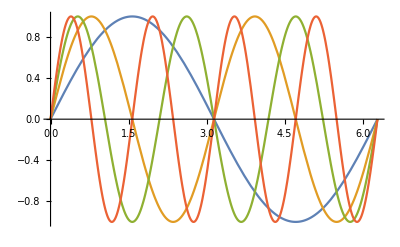

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x],Sin[4x]},{x,0,2π}]
```

```mathematica
FindRoot[{Abs[Cos[θy01] ( Cos[θy00])-√(3/80)]==0,
Abs[Cos[θy01] (- Sin[θy00])-√(77/240)]==0,
Abs[-Sin[θy01] ( Cos[θx10] Cos[θy10]+ⅈ  Sin[θx10] Sin[θy10])-√(77/240)]==0,
Abs[- Sin[θy01] (ⅈ Cos[θy10] Sin[θx10]- Cos[θx10] Sin[θy10])-√(77/240)]==0},{θx10,3},{θy00,3},{θy01,3},{θy10,3}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{θx10→-62.8319,θy00→1.90022,θy01→2.21256,θy10→2.35617}

```mathematica
{Abs[Cos[θy01] ( Cos[θy00])-√(3/80)],
Abs[Cos[θy01] (- Sin[θy00])-√(77/240)],
Abs[-Sin[θy01] ( Cos[θx10] Cos[θy10]+ⅈ  Sin[θx10] Sin[θy10])-√(77/240)],
Abs[- Sin[θy01] (ⅈ Cos[θy10] Sin[θx10]- Cos[θx10] Sin[θy10])-√(77/240)]}/.%
```

{5.55112×10^-17,0.,0.0000291636,0.0000291617}

```mathematica
testket=KroneckerProduct[ket0,ket0]
((KroneckerProduct[P1,Ry[θy10]-Id]+KroneckerProduct[Id,Id]).(KroneckerProduct[P0,Ry[θy00]-Id]+KroneckerProduct[Id,Id]).(KroneckerProduct[Ry[θy01]-Id,P0]+KroneckerProduct[Id,Id])).testket
```

KroneckerProduct[ket0,ket0]

```mathematica
ConjugateTranspose[(KroneckerProduct[Id,Id]+KroneckerProduct[P1,-Id+Ry[θy10]]).(KroneckerProduct[Id,Id]+KroneckerProduct[P0,-Id+Ry[θy00]]).(KroneckerProduct[Id,Id]+KroneckerProduct[-Id+Ry[θy01],P0])].N[{{√(3/80)},{√(77/240)},{√(77/240)},{√(77/240)}}]/.{θy00->1.900220607202805,θy01->2.212560440981948,θy10->0.75 π}
```

{{1.},{-5.55112×10^-17},{1.38778×10^-16},{5.55112×10^-17}}

```mathematica
N[{{√(3/80)},{√(77/240)},{√(77/240)},{√(77/240)}}]
```

{{0.193649},{0.566422},{0.566422},{0.566422}}

```mathematica
0.9999999997860604
```

```mathematica
{1.900220607202805,2.212560440981948,2.3561686672333844}/π
```

{0.604859,0.70428,0.749992}